```mathematica
(* Import Paclets *)
Needs["NDSolve`FEM`"]
Needs["FEMAddOns`"]
```

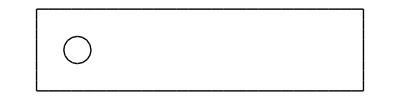

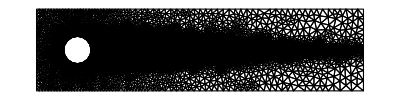

```mathematica
(* Mesh-Generation *)
c=1;
(* choose domain-size (1-length = 1-cord-length) *)
H=3; (* Domain height in cord-lengths *)
L=4*H;(* Domain Depth in cord-lengths *)
ℓ=H/2+2/10; (* Refining region core dimension in cord-lengths *)
B=H/20;
K=1/10;
Clear[x,𝓍];
𝓍rule=Solve[ℓ/(L-H/2+𝓍)==B/𝓍,𝓍];
𝓍=Abs[𝓍/.𝓍rule[[1]]];
region=ImplicitRegion[{(x^2+y^2≤(H/2)^2&& x≤0)||(x≥0&&y≤H/2&&y≥-H/2&&x≤L-H/2)},{x,y}];
Ω=RegionDifference[Rectangle[{-H/2,-H/2},{L-H/2,H/2}],Disk[{0,0},c/2]];
ΩBoundaries=ToBoundaryMesh[Ω];
ΩBoundaries["Wireframe"]
(* choose mesh-refining function *)
meshrefine[vertices_,area_]:=area>1/H;
f=Function[{vertices,area},area>1/(5 H^2) (10 Norm[Mean[vertices]])];
pred=(x^2+y^2≤(ℓ/2)^2||x≥0&&-((ℓ-B)/(H-2L))x-y≤ℓ/2&&((ℓ-B)/(H-2L))x-y≥-ℓ/2&&x≤L-H/2);
g=Function[{vertices,area},Block[{x,y},{x,y}=Mean[vertices];If[pred,area>1/(50 H^4) (0.01+1 Norm[Mean[vertices]]),area>1/(25 H^4) (0.01+10 Norm[Mean[vertices]])]]];
mesh3=ToElementMesh[ΩBoundaries,MeshQualityGoal->"Maximal",MeshRefinementFunction->g];
mesh3["Wireframe"]
```

```mathematica
M∞=2/10;
α=0;
γ=14/10;
u∞=M∞*Cos[α];
v∞=M∞*Sin[α];
ρ∞=1;
a∞=1;
p∞=1/γ;
```

```mathematica
bcs={DirichletCondition[{u[x,y]==0,v[x,y]==0},y==-H/2||y==H/2||x^2+y^2==c^2],
DirichletCondition[{u[x,y]==u∞,v[x,y]==v∞,p[x,y]==p∞},x==-H/2],
DirichletCondition[{p[x,y]==0},x==L-H/2]
};
ic={u[x,y]==0,v[x,y]==0,p[x,y]==0};
```

```mathematica
uv={u[x,y],v[x,y]}; pxy=p[x,y];
```

```mathematica
U={ρ∞,ρ∞ uv[[1]],ρ∞ uv[[2]]};
F={ρ∞ uv[[1]],ρ∞ uv[[1]]^2+ρ∞,ρ∞ uv[[1]] uv[[2]]};
G={ρ∞ uv[[2]],ρ∞ uv[[1]] uv[[2]],ρ∞ uv[[2]]^2+ρ∞};
S={0,0,0};
NS=Table[0+D[F[[i]],x]+D[G[[i]],y],{i,1,3}];
MatrixForm[NS];
pde=NS==S/.{u[x,y]->u∞,v[x,y]->v∞};
```

```mathematica
NDSolveValue[{pde,bcs},{u,v,p},{x,y}∈mesh3,Method->{"FiniteElement","InterpolationOrder"->{u->2,v->2,p->1},"IntegrationOrder"->5},WorkingPrecision->MachinePrecision]
```

NDSolveValue::femcscd: The PDE is convection dominated and the result may not be stable. Adding artificial diffusion may help.

$Aborted

```mathematica
sol=%
```

{InterpolatingFunction[{{-1., 3.}, {-1., 1.}}, <>],InterpolatingFunction[{{-1., 3.}, {-1., 1.}}, <>],InterpolatingFunction[{{-1., 3.}, {-1., 1.}}, <>]}

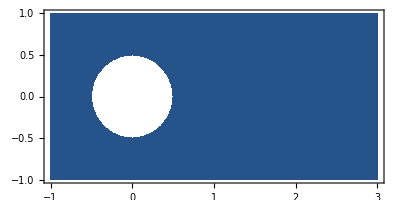

```mathematica
ContourPlot[sol[[3]][x,y],{x,y}∈Ω,AspectRatio->Automatic,Contours->20]
```

```mathematica
?ContourPlot
```

```mathematica
Do[
{ut,vt,pt}=
,{i,0,10,1}]
```

```mathematica
Do[
  {UX[i], VY[i], P0[i]} = 
   NDSolveValue[{{Inactive[
           Div][({{-UnknownSymbol, 0}, {0, -UnknownSymbol}}.Inactive[Grad][
             u[x, y], {x, y}]), {x, y}] + 
Derivative[1,0][p][x, y] + (u[x, y] - UX[i - 1][x, y])/t0 + 
         UX[i - 1][x, y]*D[u[x, y], x] + 
         VY[i - 1][x, y]*D[u[x, y], y], 
        Inactive[
           Div][({{-UnknownSymbol, 0}, {0, -UnknownSymbol}}.Inactive[Grad][
             v[x, y], {x, y}]), {x, y}] + 
Derivative[0,1][p][x, y] + (v[x, y] - VY[i - 1][x, y])/t0 + 
         UX[i - 1][x, y]*D[v[x, y], x] + 
         VY[i - 1][x, y]*D[v[x, y], y], 
Derivative[1,0][u][x, y] + 
Derivative[0,1][v][x, y]} == {0, 0, 0} /. UnknownSymbol -> UnknownSymbol, {
      DirichletCondition[{u[x, y] == U0[y, i*t0], v[x, y] == 0}, 
       x == 0.], 
      DirichletCondition[{u[x, y] == 0., v[x, y] == 0.}, 
       0 <= x <= L && y == 0 || y == H], 
      DirichletCondition[{u[x, y] == 0, 
        v[x, y] == 0}, (x - x0)^2 + (y - y0)^2 == r0^2], 
      DirichletCondition[p[x, y] == P0[i - 1][x, y], x == L]}}, {u, v,
      p}, {x, y} UnknownSymbol UnknownSymbol, 
    Method -> {"FiniteElement", 
      "InterpolationOrder" -> {u -> 2, v -> 2, p -> 1}, 
      "MeshOptions" -> {"MaxCellMeasure" -> 0.001}}], {i, 1, K}];
{ContourPlot[UX[K/2][x, y], {x, y} UnknownSymbol UnknownSymbol, 
   AspectRatio -> Automatic, ColorFunction -> "BlueGreenYellow", 
   FrameLabel -> {x, y}, PlotLegends -> Automatic, Contours -> 20, 
   PlotPoints -> 25, PlotLabel -> u, MaxRecursion -> 2], 
  ContourPlot[VY[K/2][x, y], {x, y} UnknownSymbol UnknownSymbol, 
   AspectRatio -> Automatic, ColorFunction -> "BlueGreenYellow", 
   FrameLabel -> {x, y}, PlotLegends -> Automatic, Contours -> 20, 
   PlotPoints -> 25, PlotLabel -> v, MaxRecursion -> 2, 
   PlotRange -> All]} // Quiet
{DensityPlot[UX[K][x, y], {x, y} UnknownSymbol UnknownSymbol, 
   AspectRatio -> Automatic, ColorFunction -> "BlueGreenYellow", 
   FrameLabel -> {x, y}, PlotLegends -> Automatic, PlotPoints -> 25, 
   PlotLabel -> u, MaxRecursion -> 2], 
  DensityPlot[VY[K][x, y], {x, y} UnknownSymbol UnknownSymbol, 
   AspectRatio -> Automatic, ColorFunction -> "BlueGreenYellow", 
   FrameLabel -> {x, y}, PlotLegends -> Automatic, PlotPoints -> 25, 
   PlotLabel -> v, MaxRecursion -> 2, PlotRange -> All]} // Quiet
dPl = Interpolation[
   Table[{i*t0, (P0[i][.15, .2] - P0[i][.25, .2])}, {i, 0, K, 1}]];


cD = Table[{t0*i, NIntegrate[(-UnknownSymbol*(-Sin[UnknownSymbol] (Sin[UnknownSymbol] 
Derivative[0,1][UX[i]][x0 + r Cos[], 
                 y0 + r Sin[UnknownSymbol]] + Cos[UnknownSymbol] 
Derivative[1,0][UX[i]][x0 + r Cos[UnknownSymbol], 
                 y0 + r Sin[UnknownSymbol]]) + Cos[UnknownSymbol] (Sin[UnknownSymbol] 
Derivative[0,1][VY[i]][x0 + r Cos[UnknownSymbol], 
                 y0 + r Sin[UnknownSymbol]] + Cos[UnknownSymbol] 
Derivative[1,0][VY[i]][x0 + r Cos[UnknownSymbol], 
                 y0 + r Sin[UnknownSymbol]]))*Sin[UnknownSymbol] - 
         P0[i][x0 + r Cos[UnknownSymbol], y0 + r Sin[UnknownSymbol]]*
          Cos[UnknownSymbol]) /. {r -> r0}, {UnknownSymbol, 0, 2*Pi}]}, {i, 
     1000, 2000}]; // Quiet

cL = Table[{t0*i, -NIntegrate[(-UnknownSymbol*(-Sin[UnknownSymbol] (Sin[UnknownSymbol] 
Derivative[0,1][UX[i]][x0 + r Cos[UnknownSymbol], 
                  y0 + r Sin[UnknownSymbol]] + Cos[UnknownSymbol] 
Derivative[1,0][UX[i]][x0 + r Cos[UnknownSymbol], 
                  y0 + r Sin[UnknownSymbol]]) + 
             Cos[UnknownSymbol] (Sin[UnknownSymbol] 
Derivative[0,1][VY[i]][x0 + r Cos[UnknownSymbol], 
                  y0 + r Sin[UnknownSymbol]] + Cos[UnknownSymbol] 
Derivative[1,0][VY[i]][x0 + r Cos[UnknownSymbol], 
                  y0 + r Sin[UnknownSymbol]]))*Cos[UnknownSymbol] + 
          P0[i][x0 + r Cos[UnknownSymbol], y0 + r Sin[UnknownSymbol]]*
           Sin[UnknownSymbol]) /. {r -> r0}, {UnknownSymbol, 0, 2*Pi}]}, {i, 
     1000, 2000}]; // Quiet
{ListLinePlot[cD, 
  AxesLabel -> {"t", "\!\(\*SubscriptBox[\(c\), \(D\)]\)"}], 
 ListLinePlot[cL, 
  AxesLabel -> {"t", "\!\(\*SubscriptBox[\(c\), \(L\)]\)"}], 
 Plot[dPl[x], {x, 0, 8}, AxesLabel -> {"t", "UnknownSymbolP"}]}

f002 = FindFit[cL, a*.5 + b*.8*Sin[k*16*t + c*1.], {a, b, k, c}, t]


Plot[Evaluate[a*.5 + b*.8*Sin[k*16*t + c*1.] /. f002], {t, 4, 8}, 
 Epilog -> Map[Point, cL]]

k0=k/.f002;
Struhalnumber = .1*16*k0/2/Pi


cLm = MaximalBy[cL, Last]

sol = {Max[cD[[All, 2]]], Max[cL[[All, 2]]], Struhalnumber, 
  dPl[cLm[[1, 1]] + Pi/(16*k0)]}
```

```mathematica
?Rectangle
```